## One-off file processing

## Figure out how to convert python to WL

```mathematica
ds2=ImportSequenceFile["/Users/sumner/Programming/Detexon/data/dataset_min_50_max_250_pad_300_random_85000/1.tsv"];
```

```mathematica
ds2[[1,"Output"]]//Normal//Dimensions
```

{300,3}

```mathematica
f="/Users/sumner/Programming/Detexon/data/dataset_min_50_max_250_pad_300_random_85000/0.tsv";
```

```mathematica
tsv=Import@f;
```

```mathematica
header=First@tsv;
data=Rest@tsv;
```

```mathematica
fromPythonList[listString_]:=ToExpression[StringReplace[listString,{"["->"{","]"->"}"}]];
```

```mathematica
ds=Dataset[AssociationThread[header,#]&/@data];
```

```mathematica
imgs=(*Image/@*)Transpose/@fromPythonList/@Normal[ds[All,"img"]];
pimgs=(*Image/@*)Transpose[(fromPythonList/@Normal[ds[All,"prob_img"]])[[;;,;;,1,;;]],{1,2,3}];
```

```mathematica
pimgs//First//Dimensions
```

{300,3}

```mathematica
imgAssoc=AssociationThread[Image/@imgs,Image/@pimgs];
imgAssoc[[1;;4]]
```

<|-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-|>

```mathematica
ds1=Dataset[Association@@@Partition[Riffle["Input"->#&/@imgs,"Output"->#&/@pimgs],{2}][[1;;3]]]
```

Dataset[<>]

```mathematica
inDS="Input"->#&/@imgs ;
otDs="Output"->#&/@pimgs;
```

```mathematica
ds1=<|"Input"->#[[1]],"Output"->Transpose[#[[2]],{2,1}]|>&/@Partition[Riffle[imgs,opimgs],{2}];
```

```mathematica
ds1[[1,"Output"]]//Normal//Dimensions
```

{300,3}

```mathematica
opimgs//Dimensions
```

{1700,3,300}

## Convert file to dataset

```mathematica
fromPythonList[listString_]:=ToExpression[StringReplace[listString,{"["->"{","]"->"}"}]];
pairInputsWithOutputs[inputs_,outputs_]:=Partition[Riffle["Input"->#&/@inputs,"Output"->#&/@outputs],{2}];
ImportSequenceFile[file_]:=Module[
{
tsv, header, data, ds, tds, imgs, pimgs
},
tsv = Import[file];
header = First@tsv; data = Rest@tsv;
ds=Dataset[AssociationThread[header,#]&/@data];
imgs=(*Image/@*)Transpose/@fromPythonList/@Normal[ds[All,"img"]];
pimgs=(*Image/@*)Transpose[(fromPythonList/@Normal[ds[All,"prob_img"]])[[;;,;;,1,;;]],{1,2,3}];
tds=Dataset[Association@@@pairInputsWithOutputs[imgs, pimgs]];
Return[tds];
]
ImportSequenceFiles[files_]:=Dataset[Join@@(Normal/@ImportSequenceFile/@files)]
```

```mathematica
FileNames["/Users/sumner/Programming/Detexon/data/dataset_min_50_max_250_pad_300_random_85000/*"];
```

## By hand combine smaller files into mid files (doing all at once causes crash)

```mathematica
files="/Users/sumner/Programming/Detexon/data/dataset_min_50_max_250_pad_300_random_85000/*";
dump=FileNameJoin[{NotebookDirectory[],"data","dataset.mx"}];
```

```mathematica
(*sequenceFiles=ImportSequenceFiles@FileNames[files][[91;;100]];Export[FileNameJoin[{NotebookDirectory[],"data","dataset_part_10.mx"}],sequenceFiles]*)
```

/Users/sumner/Programming/WSS2018/Detexon/data/dataset_part_10.mx

## Export everything together

```mathematica
datasets=Import/@FileNames[FileNameJoin[{NotebookDirectory[],"data","dataset_part_*.mx"}]];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"data","processed_data.mx"}],Dataset[Flatten[(Normal/@datasets)]]]
```

/Users/sumner/Programming/WSS2018/Detexon/data/processed_data.mx

## Test import

```mathematica
ds=Import@FileNameJoin[{NotebookDirectory[],"data","processed_data.mx"}];
```

```mathematica
ds=RandomSample[ds,(Round@Length@ds)*0.1];
```

```mathematica
Length@ds
```

17000

## Partition into sets

```mathematica
ratios={0.75,0.2,0.5};
ratios=Round/@(Length[ds]ratios);
trainingSet=RandomSample[ds,ratios[[1]]]; (* Use Complement to take samlpes not used already*)
validationSet=RandomSample[Complement[ds,trainingSet],ratios[[2]]];
testSet=Complement[ds,validationSet,trainingSet];
```

```mathematica
trainFile=FileNameJoin[{NotebookDirectory[],"data","1_10_train_set.mx"}];
validFile=FileNameJoin[{NotebookDirectory[],"data","1_10_valid_set.mx"}];
testFile=FileNameJoin[{NotebookDirectory[],"data","1_10_test_set.mx"}];
Export[trainFile,trainingSet];
Export[validFile,validationSet];
Export[testFile,testSet];
```

# Detexon

## Reference Model

```mathematica
ademxappReferenceModel:=NetModel["Ademxapp Model A1 Trained on Cityscapes Data"]
```

NetChain[<>]

## Simple CNN1D Block

```mathematica
AdemxappResidualCNN1DBlock[inputDimension_, name_]:=
NetGraph[
<|
name<>"_bnl_shared"->BatchNormalizationLayer["Input"-> inputDimension],
name<>"_ramp_shared"-> Ramp,
name<>"_cnn1d_branch_1"->ConvolutionLayer[2*First@inputDimension,{1}],
name<>"_cnn1d_branch_2"->ConvolutionLayer[2*First@inputDimension,{3},"PaddingSize"->{1}],
name<>"_ramp_branch_2"->ElementwiseLayer[Ramp],
name<>"_cnn1d_branch_2a"->ConvolutionLayer[2*First@inputDimension,{3},"PaddingSize"->{1}],
name<>"_plus_shared"->ThreadingLayer[Plus]
|>,
{
name<>"_bnl_shared"->name<> "_ramp_shared"-> name<>"_cnn1d_branch_1"->name<>"_plus_shared",
 name<>"_ramp_shared"->name<>"_cnn1d_branch_2"->name<>"_ramp_branch_2"->name<>"_cnn1d_branch_2a"->name<>"_plus_shared"
}
]
```

## Complex CNN1D Block

```mathematica
AdemxappResidualCNN1DBlock[inputDimension_, name_, residualBNQ_]:=With[{
scale=If[residualBNQ,2,1]
},Module[
{
residualBranch={
NetPort["Input"]->name<>"_plus_shared"
},
residualBNBranch={
name<>"_ramp_shared"-> name<>"_cnn1d_branch_1"->name<>"_plus_shared"
},
mainBranch = {
name<>"_bnl_shared"->name<>"_ramp_shared",
If[residualBNQ,
name<>"_ramp_shared"->name<>"_cnn1d_branch_main"-> name<>"_ramp_branch_main",
name<>"_ramp_shared"->name<>"_cnn1d_branch_main"->name<>"_bnl_main"-> name<>"_ramp_branch_main"
], 
name<>"_ramp_branch_main"->name<>"_cnn1d_branch_main_a"->name<>"_plus_shared"
},
residualBranchLayers=<||>,
residualBNBranchLayers=<|
name<>"_cnn1d_branch_1"->ConvolutionLayer[scale*First@inputDimension,{1}]
|>,
mainBranchLayers =<|
name<>"_bnl_shared"->BatchNormalizationLayer["Input"-> inputDimension],
name<>"_ramp_shared"-> Ramp,
name<>"_cnn1d_branch_main"->ConvolutionLayer[scale*First@inputDimension,{3},"PaddingSize"->{1}],
If[residualBNQ,Nothing,name<>"_bnl_main"->BatchNormalizationLayer[]],
name<>"_ramp_branch_main"->ElementwiseLayer[Ramp],
name<>"_cnn1d_branch_main_a"->ConvolutionLayer[scale*First@inputDimension,{3},"PaddingSize"->{1}],
name<>"_plus_shared"->ThreadingLayer[Plus]
|>,

layers, connections
},
If[residualBNQ,
layers=Join[mainBranchLayers,residualBNBranchLayers];
connections=Join[mainBranch,residualBNBranch],

layers=Join[mainBranchLayers,residualBranchLayers];
connections=Join[mainBranch,residualBranch]
];
NetGraph[layers,connections]
]]
```

## Net Definition

```mathematica
(*inputDimension=Dimensions@First@imgs;*)
net=NetGraph[<|
"conv_1a"->ConvolutionLayer[64,{3},"PaddingSize"->{1}],
"pool_1"->PoolingLayer[{3},"PaddingSize"->{1}],
"arcb_1_upsample"-> AdemxappResidualCNN1DBlock[{64, Automatic}, "arcb_1_upsample", True],
"arcb_1_res_a"-> AdemxappResidualCNN1DBlock[{128, Automatic}, "arcb_1_res_a", False],
"arcb_1_res_b"-> AdemxappResidualCNN1DBlock[{128, Automatic}, "arcb_1_res_b", False],
"pool_2"->PoolingLayer[{3},"PaddingSize"->{1}],
"arcb_2_upsample"-> AdemxappResidualCNN1DBlock[{128, Automatic}, "arcb_2_upsample", True],
"arcb_2_res_a"-> AdemxappResidualCNN1DBlock[{256, Automatic}, "arcb_2_res_a", False],
"arcb_2_res_b"-> AdemxappResidualCNN1DBlock[{256, Automatic}, "arcb_2_res_b", False],
"pool_3"->PoolingLayer[{3},"PaddingSize"->{1}],
"arcb_3_upsample"-> AdemxappResidualCNN1DBlock[{256, Automatic}, "arcb_3_upsample", True],
"arcb_3_res_a"-> AdemxappResidualCNN1DBlock[{512, Automatic}, "arcb_3_res_a", False],
"arcb_3_res_b"-> AdemxappResidualCNN1DBlock[{512, Automatic}, "arcb_3_res_b", False],
"arcb_3_res_c"-> AdemxappResidualCNN1DBlock[{512, Automatic}, "arcb_3_res_c", False],
"arcb_3_res_d"-> AdemxappResidualCNN1DBlock[{512, Automatic}, "arcb_3_res_d", False],
"arcb_3_res_e"-> AdemxappResidualCNN1DBlock[{512, Automatic}, "arcb_3_res_e", False],
"pool_4"->PoolingLayer[{3},"PaddingSize"->{1}],
"arcb_4_upsample"-> AdemxappResidualCNN1DBlock[{512, Automatic}, "arcb_4_upsample", True],
"arcb_4_res_a"-> AdemxappResidualCNN1DBlock[{1024, Automatic}, "arcb_4_res_a", False],
"arcb_4_res_b"-> AdemxappResidualCNN1DBlock[{1024, Automatic}, "arcb_4_res_b", False],
"pool_5"->PoolingLayer[{3},"PaddingSize"->{1}],
"bn_6"->BatchNormalizationLayer[],
"relu_6"->Ramp,
"conv_6"->ConvolutionLayer[512,{3},"PaddingSize"->{1}],
"relu_6a"->Ramp,
"conv_6a"->ConvolutionLayer[3,{3},"PaddingSize"->{1}],
"transpose"->TransposeLayer[],
"softmax"->SoftmaxLayer[]
|>,
{
"conv_1a"->"pool_1",
"pool_1"-> "arcb_1_upsample"->"arcb_1_res_a"->"arcb_1_res_b"-> "pool_2",
"pool_2"-> "arcb_2_upsample"->"arcb_2_res_a"->"arcb_2_res_b"-> "pool_3",
"pool_3"->"arcb_3_upsample"->"arcb_3_res_a"->"arcb_3_res_b"->"arcb_3_res_c"->"arcb_3_res_d"->"arcb_3_res_e"-> "pool_4",
"pool_4"->"arcb_4_upsample"->"arcb_4_res_a"->"arcb_4_res_b"-> "pool_5",
"pool_5"-> "bn_6"->"relu_6"->"conv_6"->"relu_6a"-> "conv_6a"->"transpose"-> "softmax"
},
"Input"->{4,300}
]
```

NetGraph[<>]

## Net Go

```mathematica
inet=NetInitialize[net];
```

```mathematica
tnet=NetTrain[inet,ds,All,LossFunction->CrossEntropyLossLayer["Probabilities"]]
```

$Aborted[]

```mathematica
ds=Import@FileNameJoin[{NotebookDirectory[],"data","test_set.mx"}];
```

```mathematica
NetInformation[inet,"LayerTypeCounts"]
```

<|ConvolutionLayer→37,PoolingLayer→5,BatchNormalizationLayer→27,ElementwiseLayer→32,ThreadingLayer→15,SoftmaxLayer→1|>

```mathematica
tNet=Import["~/Downloads/results/trained_net.wlnet"]
```

NetGraph[<>]

```mathematica
probabilitiesToClass[probMat_]:=Flatten[Ordering[#,-1]&/@probMat]
```

```mathematica
randomN[ds_]:=RandomInteger[{1,Length[ds]}];
n=randomN[ds];
Total[Abs/@(probabilitiesToClass[tNet[Normal[ds[n,"Input"]]]]-
probabilitiesToClass[Normal[ds[n,"Output"]]])]
```

297

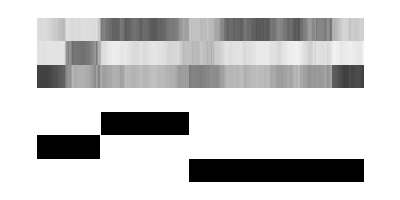

```mathematica
n=randomN[ds];
(*n=835;*)
s=Normal[ds[n]];
ArrayPlot[Join[
Transpose[tNet[s["Input"]]],
{Table[{White,Opacity[0]},300]},
Transpose[Normal[s["Output"]]]],AspectRatio->1/2]
```

```mathematica
n
```

835

```mathematica
n=randomN[ds];
s=Normal[ds[n]];
p={probabilitiesToClass[tNet[s["Input"]]]};
r={probabilitiesToClass[s["Output"]]};
With[
{
data=Join[p,{Table[{White,Opacity[0]},300]},r],
o=150
},
Manipulate[
ArrayPlot[
data[[All,i;;i+o]],
ColorFunction->"DeepSeaColors",AspectRatio->1/2
],{i,1,300-o,1}]
]
```

```mathematica
cm=ClassifierMeasurements[tNet,Normal[ds[All,"Output"]]];
```

ClassifierMeasurements::mlcntclnet: This neural network cannot be converted to a ClassifierFunction[…].

```mathematica
pm=PredictorMeasurements[tNet,Normal[ds[All,"Output"]]];
```

PredictorMeasurements::wrgfunc: The first argument should be a PredictorFunction instead of NetGraph[«1»,<|Version→11.3.5|>].

```mathematica
eval=tNet[Normal[ds[All,"Input"]]];
```

$Aborted